```mathematica
xDot[x_, y_, μ_] := μ x+y−x^2
yDot[x_,y_,μ_]:=-x+μ y +2 x^2
​​
```

​​

```mathematica
μ=.
fixPoints = Solve[{xDot[x,y,μ]==0, yDot[x,y,μ]==0},{x,y}]
```

{{x→0,y→0},{x→(1+μ^2)/(2+μ),y→(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}}

0.064

100

0.486471

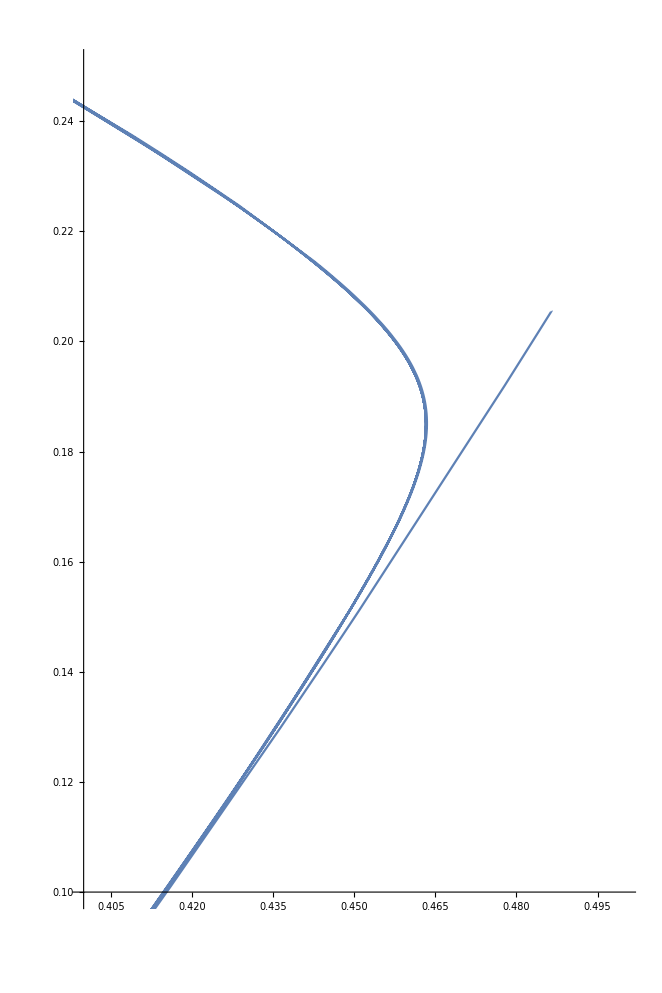

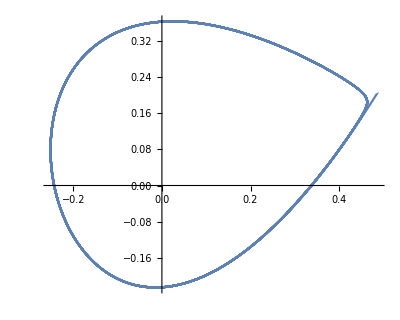

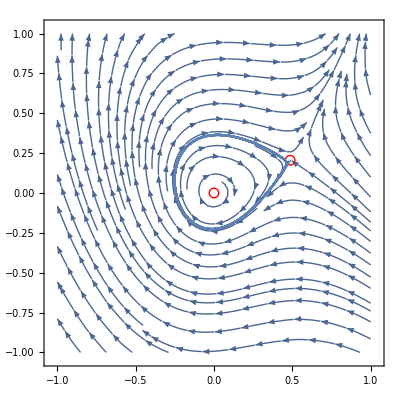

```mathematica
μ=0.064
tmax = 100
x=.
y=.
x0= (x/.fixPoints[[2]])-0.00001
y0= (y/.fixPoints[[2]]);
trajectory = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ],x[0]==x0, y[0]==y0},{x[t],y[t]},{t,0,tmax}];
 
zoomedPlot = ParametricPlot[{x[t],y[t]}/.trajectory,{t,0,tmax}, PlotRange->{{0.4,0.5},{0.1,0.25}}]
paramPlot = ParametricPlot[{x[t],y[t]}/.trajectory,{t,0,tmax}]
stream = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}];
dot1 = Graphics[{Red,Circle[Evaluate[{x,y}]/.fixPoints[[1]],0.03]}];
dot2 = Graphics[{Red,Circle[Evaluate[{x,y}]/.fixPoints[[2]],0.03]}];Show[stream,dot1,dot2, paramPlot]
```

```mathematica
0.063
```

0.063

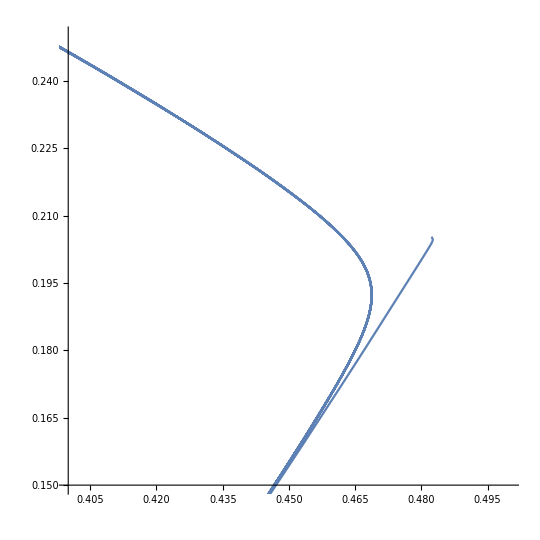

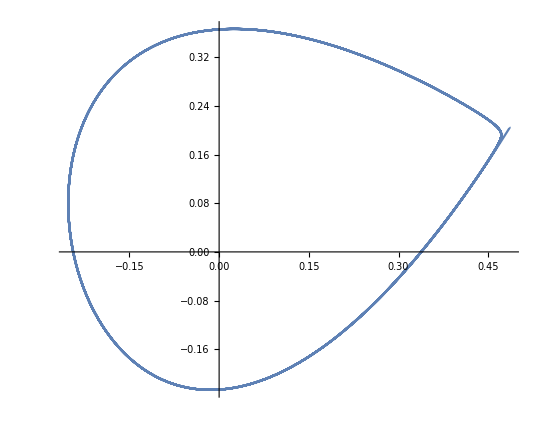

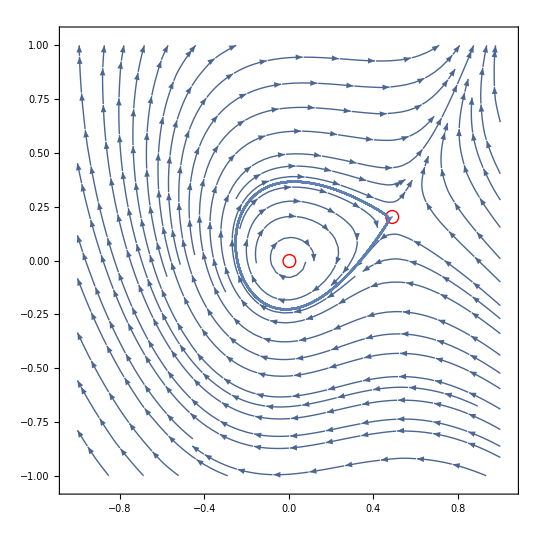

```mathematica
{x}/.fixPoints[[2]]
```

{(1+μ^2)/(2+μ)}

```mathematica
x= x/.fixPoints[[2]]-0.00000001
```

ReplaceAll::reps: {-1.×10^-8+((x/.{-1.×10^-8+(x→0.480952),-1.×10^-8+(y→0.18322)})→0.480952),-1.×10^-8+(y→0.18322)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x/.{-1.×10^-8+(x→0.480952),-1.×10^-8+(y→0.18322)}.

Hold[x/.{-1.×10^-8+(x→0.480952),-1.×10^-8+(y→0.18322)}/.{-1.×10^-8+((x/.{-1.×10^-8+(x→0.480952),-1.×10^-8+(y→0.18322)})→0.480952),-1.×10^-8+(y→0.18322)}]

```mathematica
x0= ({x}/.fixPoints[[2]])-0.00000001
```

{-1.×10^-8+(1+μ^2)/(2+μ)}

```mathematica
{x[t],y[t]}/.trajectory
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
DSolve[{x[t]==u x[t], y[t]==s y[t], x[0]==γ, y[0]==1},{x[t],y[t]},t, Assumptions->{u>0,s<0}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

```mathematica
DSolve[{x'[t]==u x[t],y'[t]==s y[t],x[0]==γ,y[0]==1},{x[t],y[t]},t,Assumptions->{u>0,s<0}]
Solve[Exp[t u] γ == 1, t]
```

{{x[t]→ⅇ^(t u) γ,y[t]→ⅇ^(s t)}}

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[1/γ])/u,C[1]∈ℤ]}}

```mathematica
DSolve[{x[t]==u x[t], x[0]==γ},{x[t]},t, Assumptions->{u>0,s<0}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

DSolve[{x[t]==u x[t],x[0]==γ},{x[t]},t,Assumptions→{u>0,s<0}]

```mathematica
μ=.
xSaddle = (1+μ^2)/(2+μ)
x=.
jacobi = {{μ-2xSaddle,1},{-1+4xSaddle,μ}}
Eigenvalues[jacobi]
```

(1+μ^2)/(2+μ)

{{μ-(2 (1+μ^2))/(2+μ),1},{-1+(4 (1+μ^2))/(2+μ),μ}}

{(-1+2 μ-√(5+9 μ^2+4 μ^3+μ^4))/(2+μ),(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)}

```mathematica
(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)//FullSimplify
```

(-1+2 μ+√(5+μ^2 (9+μ (4+μ))))/(2+μ)

{{0.008,0.0618},{0.006,0.05},{0.004,0.037}}

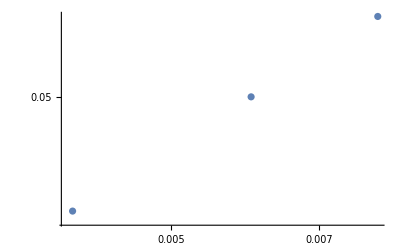

FittedModel[0.790694+0.740248 x]

2.20493 x^0.740248

```mathematica
(*gammas = {{0.003,0.486-0.4636},{0.008,0.061799999999999966},{0.002,0.023299999999999987},{0.006,0.04999999999999999},{0.001,0.01699999999999996},{0.004,0.03699999999999998}}*)
gammas = {{0.008,0.061799999999999966},{0.006,0.04999999999999999},{0.004,0.03699999999999998}}
ListLogLogPlot[gammas]
lm=LinearModelFit[Log[gammas],x,x]
f0=Normal[lm]/.x->Log[x]//Exp
```

```mathematica
{{0.003,0.486-0.4636},{0.008,0.061799999999999966},{0.002,0.023299999999999987},{0.006,0.04999999999999999},{0.001,0.01699999999999996},{0.004,0.03699999999999998}}
```

{{0.003,0.0224},{0.008,0.0618},{0.002,0.0233},{0.006,0.05},{0.001,0.017},{0.004,0.037}}

```mathematica
ⅇ*1.2
```

3.26194